# PRÁCTICA DE LABORATORIO

## CASO 1: COLA M/M/1

## PRIMERA PARTE

1. Desarrollar un sistema generador de números aleatorios basado en un generador lineal congruencial mixto que siga una distribución uniforme entre [0,1].

```mathematica
Needs["RandomData`"]
```

```mathematica
RandomData[]
```

0.773033

2. Probar el generador y demostrar mediante un histograma la bondad del generador.

```mathematica
RandomList=Table[RandomData[],{30000}];
```

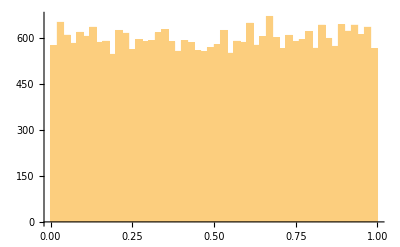

```mathematica
Histogram[RandomList,50]
```

3. Implementar el método de transformada inversa para obtener una distribución aleatoria exponencial de tiempo entre llegadas 1/λ.Representar en un histograma los valores obtenidos.

```mathematica
λ=100; (*tasa de llegadas*)
```

```mathematica
listaLlegadas=Table[RandomExp[λ],{i,30000}];
```

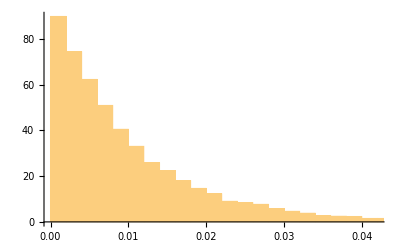

```mathematica
transfInversa=Histogram[listaLlegadas,50,PDF]
```

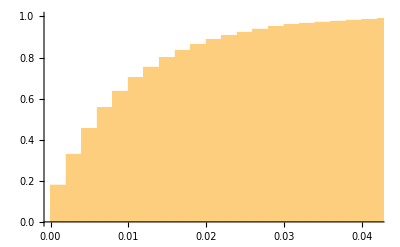

```mathematica
distrUniforme=Histogram[listaLlegadas,50,CDF]
```

```mathematica
(*FUNCIONES TEORICAS*)
F[t_]:=λ*Exp[-λ*t];
```

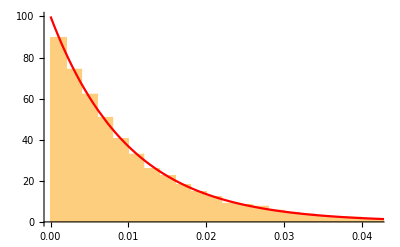

```mathematica
Show[transfInversa,Plot[F[t],{t,0,0.12},PlotStyle->Red,PlotRange->{{0,0.12},{0,λ}}]]
```

```mathematica
FUniforme[t_]:=1-Exp[-λ*t];
```

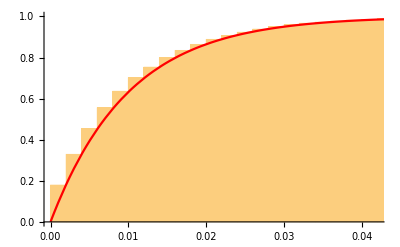

```mathematica
Show[distrUniforme,Plot[FUniforme[t],{t,0,0.1},PlotStyle->Red,PlotRange->Full]]
```

## SEGUNDA PARTE

4. Desarrollar un simulador de una cola M/M/1 con tasa λ de llegadas y de μ de servicio. Representar en un diagrama que evolucione en el tiempo el numero de usuarios en el sistema.

```mathematica
(*definición de tasa de llegadas λ y tasa de servicio μ*)
λ=100;
μ=150;
nmax=1000;
```

```mathematica
(*Tiempo entre llegadas*)
InterArrivalsTime=Table[RandomExp[λ],{nmax}];
```

```mathematica
(*Tiempo de servicio*)
ServiceTime=Table[RandomExp[μ],{nmax}];
```

```mathematica
(*Definición de la función para calcular los tiempos de llegadas desde un origen t=0*)
AcumSeries[InterArrivalsTimeList_]:=Module[{acum=0},Map[(acum=acum+#)&,InterArrivalsTimeList]];
```

```mathematica
ArrivalsTime=AcumSeries[InterArrivalsTime];
```

```mathematica
(*Definición de la función de tiempos de salida de la cola dependiendo de la política de servicio (FIFO)*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+ServiceTime[[n++]]])&/@arrivals]
```

```mathematica
(*Se calcula el tiempo entre salidas*)
DepartureTimes=FifoSchedulling[ArrivalsTime,ServiceTime];
```

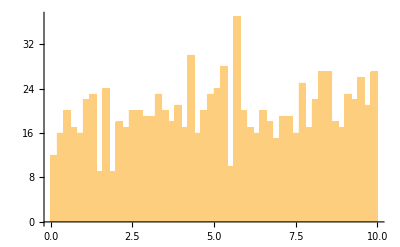

```mathematica
Histogram[DepartureTimes,50]
```

```mathematica
(*Con los tiempos de llegada y los de salida tenemos definido el funcionamiento de la cola*)
```

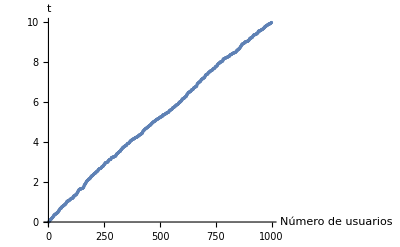

```mathematica
(*Se representa el numero de usuario en el sistema - PROBLEMA: LOS EJES ESTÁN AL REVÉS*)
ListPlot[ArrivalsTime,AxesLabel->{"Número de usuarios","t"}]
```

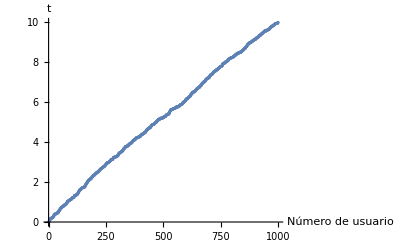

```mathematica
ListPlot[DepartureTimes,AxesLabel->{"Número de usuario","t"}]
```

```mathematica
(*CAMBIAR EJES: cambiar la lista de tiempos {time0,time1,...} por una de coordenadas {{time0,0},{time1,1},...,{timen,n}}*)
TranspArrivalTimes=Transpose[Partition[Join[ArrivalsTime,Table[i,{i,0,(nmax-1)}]],nmax]];
```

```mathematica
TranspDepartureTimes=Transpose[Partition[Join[DepartureTimes,Table[i,{i,0,(nmax-1)}]],nmax]];
```

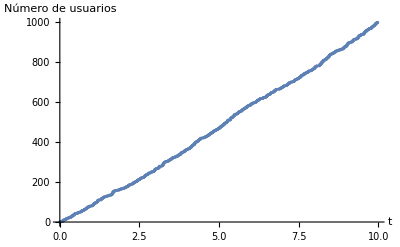

```mathematica
ListPlot[TranspArrivalTimes,AxesLabel->{"t","Número de usuarios"}]
```

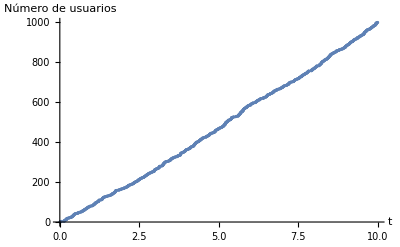

```mathematica
ListPlot[TranspDepartureTimes,AxesLabel->{"t","Número de usuarios"}]
```

```mathematica
(*Fórmula de Little*)
InterArrivalTimes=Transpose[Partition[Join[ArrivalsTime,Table[i,{i,1,nmax}]],nmax]];
```

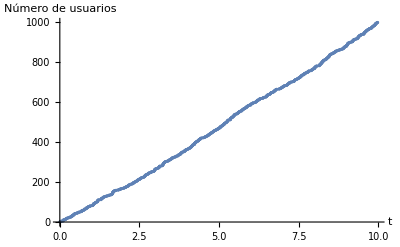

```mathematica
ListPlot[InterArrivalTimes,AxesLabel->{"t","Número de usuarios"}]
```

```mathematica
InterDepartureTimes=Transpose[Partition[Join[DepartureTimes,Table[i,{i,1,nmax}]],nmax]];
```

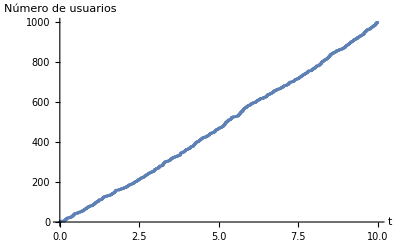

```mathematica
ListPlot[InterDepartureTimes,AxesLabel->{"t","Número de usuarios"}]
```

```mathematica
(*Igual que antes pero el índice empieza en 1 no en 0*)
PointStairStep[TranspList_,InterList_]:=Join[{{0,0}},Partition[Flatten[Transpose[Partition[Join[TranspList,InterList],nmax]]],2]];
```

```mathematica
ArrivalsStair=PointStairStep[TranspArrivalTimes,InterArrivalTimes];
```

```mathematica
DeparturesStair=PointStairStep[TranspDepartureTimes,InterDepartureTimes];
```

```mathematica
Manipulate[ListLinePlot[{ArrivalsStair[[origin;;origin+width]],DeparturesStair[[origin;;origin+width]]},AxesOrigin->{ArrivalsStair[[origin]][[1]],ArrivalsStair[[origin]][[2]]-1},PlotStyle->{Red,Blue}],{origin,1,nmax,1,Appearance->"Labeled"},{width,100,10,1}]
```

```mathematica
(*Otro método - Armando*)
PointStairStep2[list_]:=Module[{n=0},{#,n++,#,n}&/@list];
ArrivalsTimeStair=PointStairStep2[ArrivalsTime];
ArrivalsTimeStair=Partition[Flatten[ArrivalsTimeStair],2];
Insert[ArrivalsTimeStair,{0,0},1];
DepartureTimesStair=PointStairStep2[DepartureTimes];
DepartureTimesStair=Partition[Flatten[DepartureTimesStair],2];
Insert[DepartureTimesStair,{0,0},1];
```

```mathematica
Manipulate[ListLinePlot[{ArrivalsTimeStair[[origin;;origin+width]],
DepartureTimesStair[[origin;;origin+width]]},AxesOrigin->{ArrivalsTimeStair[[origin]][[1]],ArrivalsTimeStair[[origin]][[2]]-1},PlotStyle->{Red,Blue}],{origin,1,1000,1},{width,100,10,1}]
```

5. Representar el tiempo medio de espera en el sistema normalizado por µ para diferentes valores de ρ. Hacerlo con la curva teórica y representar los puntos obtenidos en las simulaciones.

```mathematica
(*número de usuarios en el sistema en cada instante de tiempo*)
llegadas = {#,1}&/@ArrivalsTime;
```

```mathematica
salidas={#,-1}&/@DepartureTimes;
```

```mathematica
ArrayEventos=Sort[Join[llegadas,salidas],#1[[1]]<#2[[1]]&];
```

```mathematica
userInSystem[list_]:=Module[{n=0,lastTime=0},Flatten[Map[{{lastTime,n},{lastTime=#[[1]],If [#[[2]]==1,n++,n--]}}&,list],1]];
```

```mathematica
listUsers=userInSystem[ArrayEventos];
```

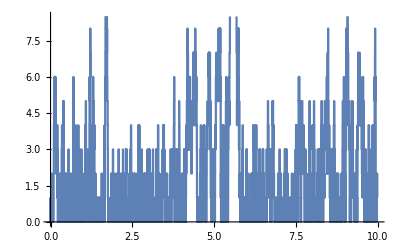

```mathematica
ListLinePlot[listUsers]
```

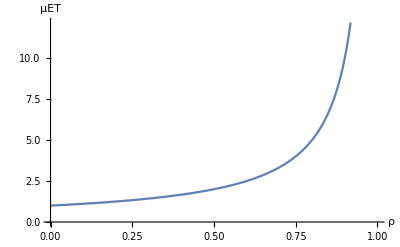

```mathematica
(*tiempo medio de espera en el sistema*)
Plot[1/(1-ρ),{ρ,0,1},AxesOrigin->{0,0},AxesLabel->{ρ,µET}]
```

```mathematica
GetMeanTime[ArrivalTimes_,DepartureTimes_]:=Module[{EstanciaMedia={}},For[n=1,n≤Length[ArrivalTimes],n++,EstanciaMedia=Insert[EstanciaMedia,DepartureTimes[[n]]-ArrivalTimes[[n]],n]]; Total[EstanciaMedia]/Length[EstanciaMedia]];
```

```mathematica
ServiceMeanTime=GetMeanTime[ArrivalsTime,DepartureTimes]//N
```

0.0200315

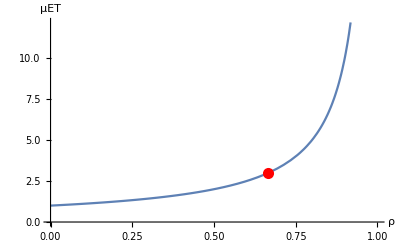

```mathematica
Show[Plot[1/(1-ρ),{ρ,0,1},AxesOrigin->{0,0},AxesLabel->{ρ,µET}],Graphics[{PointSize[0.02],Red,Point[{λ/μ,ServiceMeanTime*μ}]}]]
```

```mathematica
interArrivalTimes[λ_]:=Table[RandomExp[λ],{nmax}];
```

```mathematica
serviceTime[μ_]:=Table[RandomExp[μ],{nmax}];
```

```mathematica
acumSeries[list_]:=Module[{acum=0},Map[(acum=acum+#)&,list]];
```

```mathematica
arrivalTimes[λ_]:=acumSeries[interArrivalTimes[λ]];
```

```mathematica
departureTimes[λ_,μ_]:=FifoSchedulling[arrivalTimes[λ],serviceTime[μ]];
```

```mathematica
ρ[λ_,μ_]:=λ/μ;
```

```mathematica
Manipulate[Show[Plot[1/(1-ρ),{ρ,0,1},AxesOrigin->{0,0},AxesLabel->{ρ,µET}],Graphics[{PointSize[0.02],Red,Point[{λ/μ,ServiceMeanTime*μ}]}]],{λ,10,1000,10},{μ,10,1000,10}]
```

```mathematica
NO ESTA BIEN!
```

ESTA NO BIEN!

## TERCERA PARTE

6. Representar las probabilidades de estado pn de la cola M/M/1 teóricas, así como las obtenidas por simulación para diferentes puntos de ensayo. Comprobar si esa distribución coincide con la visualizada según la propiedad PASTA en los tiempos de llegada.

```mathematica
RandomExp2[tasa_]:=Log[e,RandomReal[]]/(-tasa)//N;
```

```mathematica
interArrivalTimes2[t_,nmax_]:=Table[RandomExp2[t],{nmax}];
```

```mathematica
serviceTime2[y_,nmax_]:=Table[RandomExp2[y],{nmax}];
```

```mathematica
acumSeries2[l_]:=Module[{acum=0},Map[(acum=acum+#)&,l]];
```

```mathematica
departureTimes2[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals];
```

```mathematica
numUsuarios[arrivals_,departures_]:=Modules[{},tiempos=Map[{1,#}&,arrivals];
tiempos=Partition[Flatten[Insert[tiempos,Map[{-1,#}&,departures],Length[tiempos]+1]],2];tiempos=Sort[tiempos,#1[[2]]<#2[[2]]&];NumUsuariosTiempo=Module[{},i=0;Map[{#[[2]],i+=#[[1]]}&,tiempos]];
NumUsuariosTiempoIntermedio=MapThread[{#1[[1]],If[#2[[1]]==1,#1[[2]]-1,#1[[2]]+1]}&,{NumUsuariosTiempo,tiempos}];UsuariosT=Partition[Flatten[MapThread[{#2,#1}&,{NumUsuarioTiempo.NumUsuariosTiempoIntermedio}]],2]];
```

```mathematica
UsuariosXinstante[λ_,μ_,muestras_]:=Module[{},InterArrivalT=interArrivalTimes2[λ,muestras];
ServiceT=serviceTime2[μ,muestras];ArrivalsT=acumSeries2[InterArrivalT];DepartureT=departureTimes2[ArrivalsT,ServiceT];
UsuariosT=numUsuarios[ArrivalsT,DepartureT];UsuariosT]
```

```mathematica
muestras=10000;
```

```mathematica
gUsuariosTiempo[λ_,μ_]:=Module[{},usuariosInstante=UsuariosXinstante[λ,μ,muestras];Manipulate[Show[ListLinePlot[Take[usuariosInstante,{origin,origin+width}]],ImageSize->Large],{width,10,1000,1},{origin,1,muestras-1000,1}]]
```

```mathematica
muestras=10000;
```

```mathematica
fArrayEstados[usuariosInstante_]:=Module[{},
arrayEstados=Table[0,{51}];(*en el 51 agrupamos los demás*)

For[i=1,i<=Length[usuariosInstante],i+=2,
If[usuariosInstante[[i]][[2]]+1>50,++arrayEstados[[51]],++arrayEstados[[usuariosInstante[[i]][[2]]+1]]]
];arrayEstados]
```

```mathematica
Teorico[ρ_]:=DiscretePlot[If[ρ==1||ρ==0,0,(1-ρ)/(1-ρ^(51+1))*ρ^n],{n,0,51,1},PlotStyle->{Blue,Thick}]
```

```mathematica
PASTA[λ_,μ_]:=Module[{},
usuariosInstante=UsuariosXinstante[λ,μ,muestras];
arrayEstados=fArrayEstados[usuariosInstante];
probEstados=Module[{},i=0;Map[{i++,#/Length[usuariosInstante/2]}&,arrayEstados]];
Show[ListPlot[probEstados,PlotRange->{-0.1,0.6},ImageSize->Large,PlotStyle->Green],Teorico[λ/μ]
]
]
```

```mathematica
PASTA[1,10]
```

PASTA[1,10]